## Method 1: Bots

```mathematica
ClearAll["Global`*"]
```

```mathematica
gridSize=20;

positions=Flatten[
Table[{x,y},{x,1,gridSize},{y,1,gridSize}],
1
];
```

```mathematica
Length[positions]
```

400

```mathematica
strategies=RandomChoice[{0.5,0.5}->{1,0},Length[positions]];
```

```mathematica
{{x,y},strategy}
```

{{x,y},strategy}

```mathematica
bots=MapThread[{#1,#2}&,{positions,strategies}];
```

```mathematica
getPositions[bots_]:=bots[[All,1]]
getStrategies[bots_]:=bots[[All,2]]
```

## Testing / Checks

```mathematica
AllTrue[bots,VectorQ[#[[1]],IntegerQ]&&MemberQ[{0,1},#[[2]]]&]
```

True

```mathematica
Union[getPositions[bots]]===positions
```

True

```mathematica
Length[bots]==20*20
```

True

```mathematica
ListPlot[{Pick[getPositions[bots],getStrategies[bots],1],Pick[getPositions[bots],getStrategies[bots],0]},PlotStyle->{Blue,Red},AspectRatio->1,PlotRange->{{0,21},{0,21}},Axes->True]
```

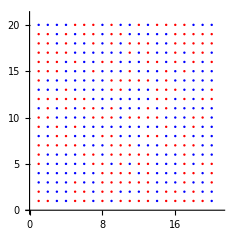

## Method 2: Mover

```mathematica
(*This is just a grid geometry helper to define how space works in the model*)
(*Moore Neighborhood*)
```

```mathematica
gridSize=20;

neighbors[{x_,y_}]:=
Select[
{{x-1,y-1},{x-1,y},{x-1,y+1},
{x,y-1},                               {x,y+1},
{x+1,y-1},{x+1,y},{x+1,y+1}
},
1<=#[[1]]<=gridSize&&1<=#[[2]]<=gridSize&]
(*Quick test of this...*)
neighbors[{1,1}]
```

{{1,2},{2,1},{2,2}}

```mathematica
(*It returned only valid in-bound neighbors so we're good so far*)
```

```mathematica
(*Now for the movement probability by strategy. This is a behavioral assumption,
I can tune these later*)
```

```mathematica
moveProb[strategy_]:=
If[strategy==1,
0.1,(*cooperators move rarely*)
0.4    (*defectors move more*)
]
```

```mathematica
(*Now for the actual core mover*)
```

```mathematica
moveBots[bots_]:=Module[{positions,strategies,wantsMove,newPositions,order,pos,nbrs,target,occupied,i},positions=getPositions[bots];
strategies=getStrategies[bots];
newPositions=positions;
wantsMove=MapThread[#1<#2&,{RandomReal[{0,1},Length[bots]],moveProb/@strategies}];
order=RandomSample[Range[Length[bots]]];
occupied=AssociationThread[newPositions->Range[Length[bots]]];

Do[i=order[[k]];
If[wantsMove[[i]],pos=newPositions[[i]];
nbrs=neighbors[pos];
nbrs=Select[nbrs,!KeyExistsQ[occupied,#]&];
If[nbrs=!={},target=RandomChoice[nbrs];
newPositions[[i]]=target;
KeyDropFrom[occupied,pos];
occupied[target]=i;];],{k,Length[order]}];
MapThread[{#1,#2}&,{newPositions,strategies}]]
```

```mathematica
(*Now we'll test the mover in isolation*)
Clear[moveProb]
```

```mathematica
moveProb[1]:=0.2;  (*cooperators*)
moveProb[0]:=0.6;  (*defectors*)
moveProb/@{0,1,1,0}
```

{0.6,0.2,0.2,0.6}

```mathematica
bots=Table[{
{RandomInteger[{1,20}],RandomInteger[{1,20}]}, (*position*)
RandomChoice[{0,1}] (*strategy*)
},{50} (*number of bots for testing*)
];
```

```mathematica
bots2=moveBots[bots];
```

```mathematica
AllTrue[getPositions[bots2],1<=#[[1]]<=20&&1<=#[[2]]<=20&]
```

True

```mathematica
Length[bots2]==Length[bots]
```

True

```mathematica
getStrategies[bots2]===getStrategies[bots]
```

True

```mathematica
Length[Union[getPositions[bots2]]]==Length[bots2]
```

True

```mathematica
(*Quick visual check*)
```

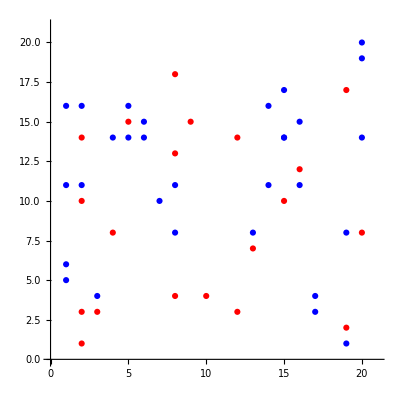

```mathematica
ListPlot[
{
Pick[getPositions[bots2],getStrategies[bots2],1],Pick[getPositions[bots2],getStrategies[bots2],0]
},
PlotStyle->{Blue,Red},
PlotRange->{{0,21},{0,21}},
AspectRatio->1
]
```